```mathematica
km=10^5 cm
kpc = 1000 pc
pc=3.0857*10^18 cm
Mo=1.989*10^33 g
G=6.672*10^-8  cm^3 g^-1 s^-2
σr=30 km s^-1
Ω=229 /8  km s^-1 kpc^-1
Σ=70 Mo/pc^2
κ=1.35Ω 
(σr κ)/(3.26 G Σ)
2π/3.36
```

100000 cm

3.0857×10^21 cm

3.0857×10^18 cm

1.989×10^33 g

(6.672×10^-8 cm^3)/(g s^2)

(3000000 cm)/s

(9.27666×10^-16)/s

(0.0146226 g)/cm^2

(1.25235×10^-15)/s

1.18127

1.87

```mathematica
Remove["Global`*"]
Mga =  Vc^2  Log[ra/ro]
Mgp=  Vc^2  Log[rp/ro]

va=va/.Solve[{Md va ra == Md vp rp},va][[1]]
vp/.Solve[{1/2 Md va^2-G Mga Md/ra ==1/2 Md vp^2-G Mgp Md/rp},vp][[2]]
Assuming[Md>0&&vp>0&&Vc>0&&ro>0&&ra>rp,FullSimplify[Expand[PowerExpand[Simplify[PowerExpand[(%)^2]]]]]]
Solve[%%==Vc^2,r][[1]]/.ra->(5 rp)
```

Vc^2 Log[ra/ro]

Vc^2 Log[rp/ro]

(rp vp)/ra

(√2 √(-G rp Vc^2 Log[ra/ro]+G ra Vc^2 Log[rp/ro]))/(√(ra rp-rp^3/ra))

(2 G ra Vc^2 (rp Log[ra]+(ra-rp) Log[ro]-ra Log[rp]))/(-ra^2 rp+rp^3)

{}

```mathematica
{-(G Md Mga)/ra+(Md rp^2 vp^2)/(2 ra^2)==-(G Md Mgp)/rp+(Md vp^2)/2}
```

{-(G Md Mga)/ra+(Md rp^2 vp^2)/(2 ra^2)==-(G Md Mgp)/rp+(Md vp^2)/2}

```mathematica
Integrate[vc^2/(4 π G r^2)
```

1/2 Rmax (1-Cos[θ])

(√(Rmax^3/(G M)) (θ-Sin[θ]))/(2 √2)

(√2 √((G M)/Rmax) Sin[θ])/(1-Cos[θ])

((θ-Sin[θ]) Sin[θ])/(-1+Cos[θ])^2

-118000.

150000000000000000 π

2.13×10^22

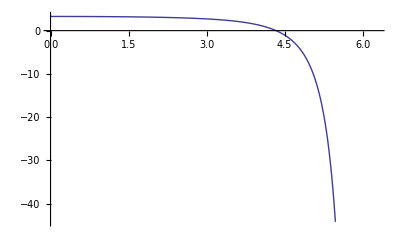

{{θ→4.33449}}

{7.04642×10^39}

{(3.52321×10^6)/}

```mathematica
Remove["Global`*"]
A=(Rmax/2);
B=√(A^3/(G M));
r=A(1-Cos[θ])
t=B(θ-Sin[θ])
v=((2 G M)/Rmax)^(1/2)(Sin[θ]/(1-Cos[θ]))
Assuming[G>0&&M>0&&Rmax>0,Simplify[(v t)/r]]
v=-1.18*10^5
tu=15*10^9 π 10^7
d=7.1 10^3 3*10^18

Plot[(Sin[θ](θ-Sin[θ]))/(1-Cos[θ])^2-(v tu)/d,{θ,0,2π}]
Solve[{(Sin[θ](θ-Sin[θ]))/(1-Cos[θ])^2-(v tu)/d==0,0≤θ≤2π},θ]
(d/(1-Cos[θ]))^3/((tu/(θ-Sin[θ]))^2(6.67*10^-8))/.%
%/(2*10^33)
```